```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=Read[StringToStream[input[[4]]]];
nStore=Read[StringToStream[input[[6]]]];
nTrajectory=Read[StringToStream[input[[8]]]];
nBin=Read[StringToStream[input[[10]]]];
yWall=Read[StringToStream[input[[12]]]];
lambda=Read[StringToStream[input[[14]]]];
deltaZ=Read[StringToStream[input[[16]]]];
deltaPz=Read[StringToStream[input[[18]]]];
transitTime=Read[StringToStream[input[[20]]]];
density=Read[StringToStream[input[[22]]]];
rabi=Read[StringToStream[input[[24]]]];
kappa=Read[StringToStream[input[[26]]]];
invT2 = Read[StringToStream[input[[28]]]];
controlType = input[[30]];
name =input[[32]]
```

dt0.01_dZ0_dPz0_tau1.0_nBin30_dens100_g3_k90_yWall1.0

```mathematica
(*Define steady states*)
```

```mathematica
steadyMultiplier = 15;
t0=steadyMultiplier*transitTime;
n0=N[Ceiling[t0/tmax*nStore]];
```

```mathematica
n0
```

```mathematica
Ceiling[(15. "1.0" "1000")/("20")]
```

Ceiling[(15. 1.0 1000)/20]

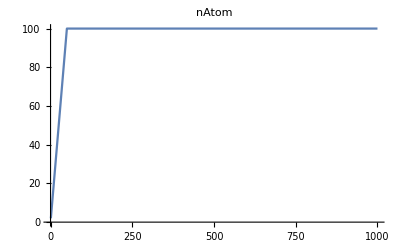

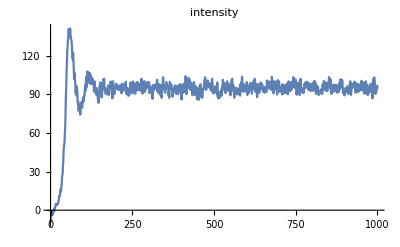

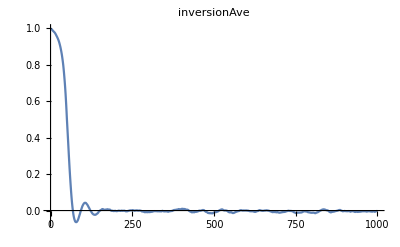

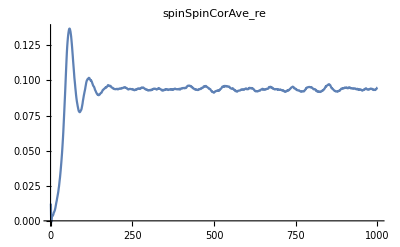

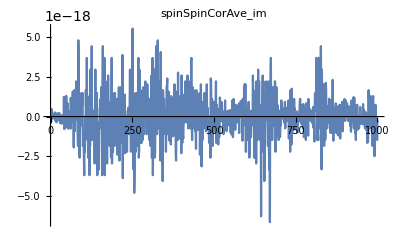

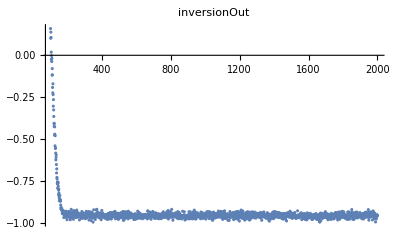

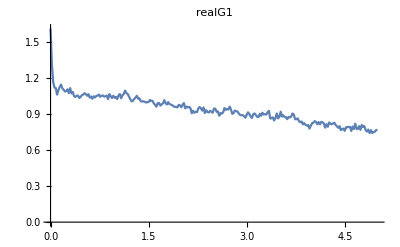

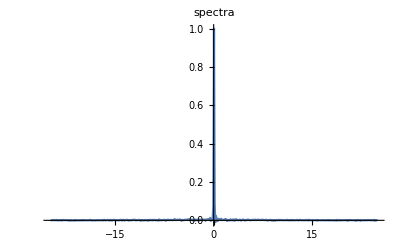

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>controlType <>"/"<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_im.dat"]];
spinSpinCorRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_re.dat"]];
spinSpinCorIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_im.dat"]];
szMatrix=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szMatrix.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

```mathematica
(*Getting steady-state values*)
nAtomSS=Take[nAtom,-5]
```

{100,100,100,100,100}

FittedModel[1.52758/(1.91211+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 1.38279 | 0.0648862 | 21.311 | 3.86423×10^-72
A | 1.10471 | 0.0366544 | 30.1384 | 1.99026×10^-114

1.38279

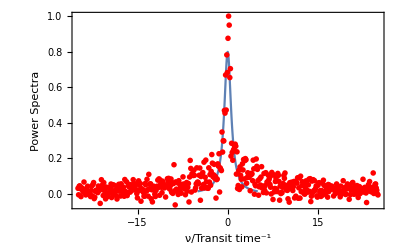

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-5,5},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

0.230194

B ⅇ^(-t/tc)

FittedModel[0.426269 ⅇ^(-5.46078 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 0.183124 | 0.0103378 | 17.7141 | 5.46638×10^-46
B | 0.426269 | 0.0161274 | 26.4314 | 3.19823×10^-74

0.183124

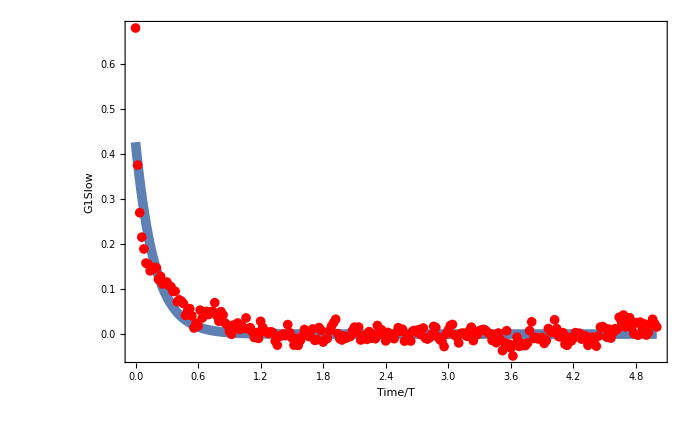

```mathematica
(*Fit the G1 function to exponential*)
c1=-kappa/2;
c2=-rabi/2;
c3=-rabi/2*;
c4=0;



exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

1.73822

```mathematica
(*Notice there is another exponential decay.*)
```

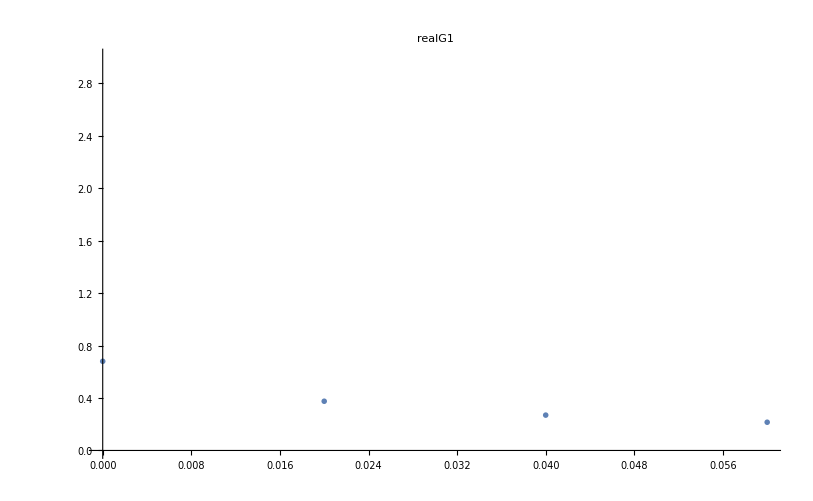

B2 ⅇ^(-linewidthQuick π t)

FittedModel[0.670881 ⅇ^(-25.2046 t)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidthQuick | 8.02288 | 1.18998 | 6.74205 | 0.0937418
B2 | 0.670881 | 0.0388245 | 17.2798 | 0.0368007

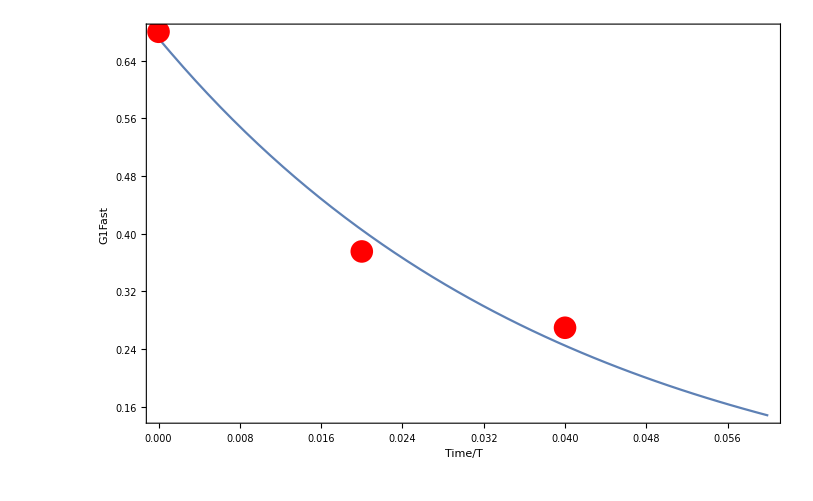

```mathematica
cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(linewidthQuick Pi)/.fitExp2["BestFitParameters"]
```

0.0396753

```mathematica
Mean[intensity[[-200;;]]]
```

11.7779

```mathematica
ListLinePlot[ 100*(1-szFinal)]
```

-Graphics-